```mathematica
SetDirectory@NotebookDirectory[];
Import["path to QuESTlink.m"];
CreateLocalQuESTEnv["path to quest_link"];
(*Read the paper [Tyson Jones and Simon Benjamin, arXiv:1912.07904] for how to setup the environment.*)
```

## Parameters

```mathematica
numQb=3;
PI=N[π,12];
```

## QC

```mathematica
ψIN=CreateQureg[numQb];
ψOUT=CreateQureg[numQb];
ψWP=CreateQureg[numQb];
```

## Basis

```mathematica
ProNeurons[OUT_]:=(
Pro={OUT[[1]]+OUT[[3]]+OUT[[5]]+OUT[[7]],OUT[[2]]+OUT[[4]]+OUT[[6]]+OUT[[8]]};
Return[Pro]
)
```

## Neural Network Cirucit

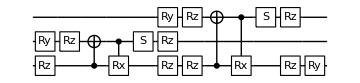

```mathematica
circuitNN[θlist_]:=(
circNN={};

ϕ=θlist[[1]];
θ=θlist[[2]];
a=0;b=1;
circMR={Subscript[Rz, a][θ],Subscript[Rz, b][θ],Subscript[C, a][Subscript[X, b]],Subscript[C, b][Subscript[Rx, a][PI-2θ]],Subscript[S, b],Subscript[Rz, b][-θ],Subscript[Rz, a][-θ]};
circNN=Join[circNN,{Subscript[Ry, b][ϕ]},circMR];

ϕ=θlist[[3]];
θ=θlist[[4]];
a=0;b=2;
circMR={Subscript[Rz, a][θ],Subscript[Rz, b][θ],Subscript[C, a][Subscript[X, b]],Subscript[C, b][Subscript[Rx, a][PI-2θ]],Subscript[S, b],Subscript[Rz, b][-θ],Subscript[Rz, a][-θ]};
circNN=Join[circNN,{Subscript[Ry, b][ϕ]},circMR];

ϕ=θlist[[5]];
a=0;
circNN=Join[circNN,{Subscript[Ry, a][ϕ]}];

Return[circNN]
)
circNN=circuitNN[Table[i/10,{i,1,5}]];
DrawCircuit@circNN
```

## Distance

```mathematica
circNeurons={Subscript[H, 0]};
DrawCircuit@circNeurons
circGHZ={Subscript[H, 1],Subscript[C, 1][Subscript[X, 2]]};
DrawCircuit@circGHZ
circPLUS={Subscript[H, 1],Subscript[H, 2]};
DrawCircuit@circPLUS
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Clear[Distance]
Distance[θlist_/;(And@@(NumericQ/@θlist))]:=(
circNN=circuitNN[θlist];

circ=Join[circNeurons,circGHZ,circNN];
ApplyCircuit[circ,ψIN,ψOUT];
OUT=Abs[GetQuregMatrix[ψOUT]]^2;
ProGHZ=ProNeurons[OUT];

circ=Join[circNeurons,circPLUS,circNN];
ApplyCircuit[circ,ψIN,ψOUT];
OUT=Abs[GetQuregMatrix[ψOUT]]^2;
ProPLUS=ProNeurons[OUT];

Dis=Total[Abs[ProGHZ-ProPLUS]]/2;

Return[Dis]
)
Distance[Table[0,{i,1,5}]]
ProGHZ
ProPLUS
```

0.

{0.5,0.5}

{0.5,0.5}

## Find

{0.707107,{0_1→1.5708,0_2→4.42954×10^-8,0_3→1.5708,0_4→-4.59834×10^-8,0_5→-0.785398}}

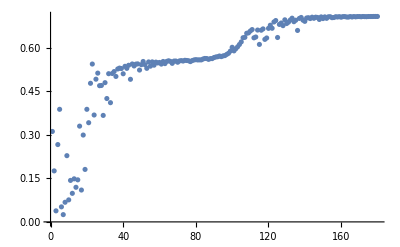

```mathematica
θlist=Table[Subscript[θ, i],{i,1,5}];
{res,data}=Reap[NMaximize[Distance[θlist],θlist,EvaluationMonitor:>Sow[Distance[θlist]]]];
res
plot=ListPlot[data]
```

## Optimal Parameters

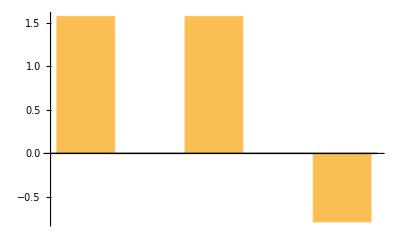

0.707107

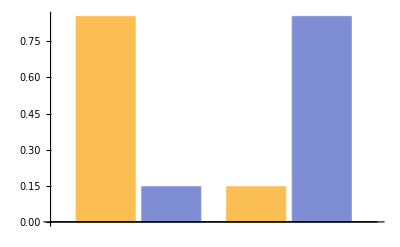

```mathematica
plotθlist=BarChart[θlist/.Last[res]]
Distance[θlist/.Last[res]]
ProGP=Table[{ProGHZ[[i]],ProPLUS[[i]]},{i,1,2}];
plotPro=BarChart[ProGP]
```

## Data and Plot

```mathematica
file=File["Ising_find-3q.dat"];
toFile={};
AppendTo[toFile,"Optimal distance:"];
AppendTo[toFile,res[[1]]];
AppendTo[toFile,""];
AppendTo[toFile,"Optimal parameters:"];
AppendTo[toFile,θlist/.Last[res]];
AppendTo[toFile,""];
AppendTo[toFile,"Evaluations:"];
AppendTo[toFile,data];
AppendTo[toFile,""];
Export[file,toFile];
```

```mathematica
DisC=N[2(1/2-1/2^2)+(2^2-2)/2^2,12]/2
Fid=N[1/(√2),12]
DisQ=N[√(1-Fid^2),12]
```

0.5

0.707106781187

0.707106781187

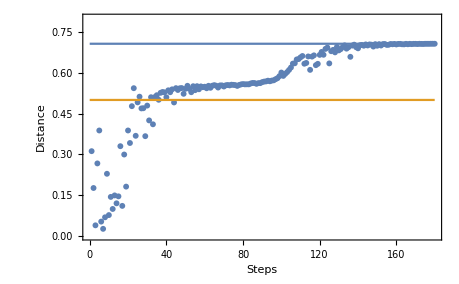

```mathematica
plot=ListPlot[Transpose[{Range[1,Length[data[[1]]]],data[[1]]}],PlotRange->{{0,Length[data[[1]]]},{0,0.8}},Axes->{False,False},Frame->True,FrameLabel->{"Steps","Distance"},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->{460,Automatic},LabelStyle->{FontSize->18}];
plotQC=ListLinePlot[{{{0,DisQ},{Length[data[[1]]],DisQ}},{{0,DisC},{Length[data[[1]]],DisC}}}];
Show[plot,plotQC]
```

```mathematica
θlist/.Last[res]
```

{1.5708,4.42954×10^-8,1.5708,-4.59834×10^-8,-0.785398}